## Square Profits 1/5/21 - 1/25/21, Personal Checking 2892

```mathematica
Profit210101thru0125 = Plus[29.12,512.34,923.80,565.93,682.66,628.99,573.44,756.41,635.62,563.20,430.21,243.20,781.58,790.25]
```

8116.75

```mathematica
TotalDaysLen1 = Length[{29.12,512.34,923.80,565.93,682.66,628.99,573.44,756.41,635.62,563.20,430.21,243.20,781.58,790.25}]
```

14

```mathematica
Profit1 = {29.12,512.34,923.80,565.93,682.66,628.99,573.44,756.41,635.62,563.20,430.21,243.20,781.58,790.25};
```

```mathematica
Sort[Profit1]
```

{29.12,243.2,430.21,512.34,563.2,565.93,573.44,628.99,635.62,682.66,756.41,781.58,790.25,923.8}

```mathematica
%//StandardForm
```

{29.12,243.2,430.21,512.34,563.2,565.93,573.44,628.99,635.62,682.66,756.41,781.58,790.25,923.8}

## Square Profits 1/26/21 - 8/18/21, Business Checking 8775

```mathematica
Profit210126thru0818=934.89+928.98+894.33+893.44+890.12+887.30+885.16+875.23+846.99+846.79+846.00+840.07+833.88+817.68+812.06+810.12+802.13+794.48+790.25+781.58+780.17+776.61+774.57+770.04+762.01+759.33+757.28+755.82+748.98+744.23+743.15+741.06+731.46+723.43+723.17+722.22+705.75+705.07+696.75+689.88+686.27+686.18+684.99+682.85+680.91+678.38+671.95+663.58+663.00+652.08+634.80+633.66+630.76+629.79+623.55+618.44+614.58+610.53+601.52+600.03+599.10+596.85+591.55+590.23+572.10+558.48+551.77+549.90+548.93+546.10+540.07+528.24+519.82+511.44+507.74+499.11+487.19+485.38+475.11+469.93+458.45+452.37+450.56+445.40+443.95+439.56+436.06+434.35+432.16+430.21+414.53+407.31+402.25+395.53+373.82+357.46+341.58+341.19+310.70+307.64+306.13+305.78+304.56+299.84+282.12+277.88+276.26+243.20+197.03+180.97+111.91
```

66360.1

```mathematica
TotalDays = 111;
AverageDailyProfit = Profit210101thru0818/TotalDays
```

597.839

```mathematica
TotalDaysLen2 = Length[{934.89,928.98,894.33,893.44,890.12,887.30,885.16,875.23,846.99,846.79,846.00,840.07,833.88,817.68,812.06,810.12,802.13,794.48,790.25,781.58,780.17,776.61,774.57,770.04,762.01,759.33,757.28,755.82,748.98,744.23,743.15,741.06,731.46,723.43,723.17,722.22,705.75,705.07,696.75,689.88,686.27,686.18,684.99,682.85,680.91,678.38,671.95,663.58,663.00,652.08,634.80,633.66,630.76,629.79,623.55,618.44,614.58,610.53,601.52,600.03,599.10,596.85,591.55,590.23,572.10,558.48,551.77,549.90,548.93,546.10,540.07,528.24,519.82,511.44,507.74,499.11,487.19,485.38,475.11,469.93,458.45,452.37,450.56,445.40,443.95,439.56,436.06,434.35,432.16,430.21,414.53,407.31,402.25,395.53,373.82,357.46,341.58,341.19,310.70,307.64,306.13,305.78,304.56,299.84,282.12,277.88,276.26,243.20,197.03,180.97,111.91}]
```

111

```mathematica
Profit2 = {934.89,928.98,894.33,893.44,890.12,887.30,885.16,875.23,846.99,846.79,846.00,840.07,833.88,817.68,812.06,810.12,802.13,794.48,790.25,781.58,780.17,776.61,774.57,770.04,762.01,759.33,757.28,755.82,748.98,744.23,743.15,741.06,731.46,723.43,723.17,722.22,705.75,705.07,696.75,689.88,686.27,686.18,684.99,682.85,680.91,678.38,671.95,663.58,663.00,652.08,634.80,633.66,630.76,629.79,623.55,618.44,614.58,610.53,601.52,600.03,599.10,596.85,591.55,590.23,572.10,558.48,551.77,549.90,548.93,546.10,540.07,528.24,519.82,511.44,507.74,499.11,487.19,485.38,475.11,469.93,458.45,452.37,450.56,445.40,443.95,439.56,436.06,434.35,432.16,430.21,414.53,407.31,402.25,395.53,373.82,357.46,341.58,341.19,310.70,307.64,306.13,305.78,304.56,299.84,282.12,277.88,276.26,243.20,197.03,180.97,111.91};
```

```mathematica
ProfitTotal=Join[Profit1,Profit2];
TotalDaysLen=Length[ProfitTotal]
Profit210126thru0818x=Total[Profit2] 
Profit210105thru0818x=Profit210101thru0125 +Profit210126thru0818x
AverageDailyProfitx = Profit210105thru0818x/TotalDaysLen
Mean[ProfitTotal]
medianDailyProfit = Median[ProfitTotal]
```

125

66360.1

74476.9

595.815

595.815

618.44

```mathematica
projectedAvg = 74*AverageDailyProfitx
projectedYearTotal = Profit210105thru0818x + projectedAvg
projectedMedian = 74*medianDailyProfit
projectedYearTotalMed = Profit210105thru0818x + projectedMedian
```

44090.3

118567.

45764.6

120241.

It has been 33 Weeks and 2 days so far so (52  - 33) weeks < 19 weeks left 
33 weeks x 4 days/week= 132 days expected, 19 weeks x 4 days/week= (76 - 2) days left projected

```mathematica
Len900plus =Length[{934.89,928.98,923.80}]
Len800plus =Length[{894.33,893.44,890.12,887.30,885.16,875.23,846.99,846.79,846.00,840.07,833.88,817.68,812.06,810.12,802.13}]
Len700plus =Length[{794.48,790.25,781.58,780.17,776.61,774.57,770.04,762.01,759.33,757.28,755.82,748.98,744.23,743.15,741.06,731.46,723.43,723.17,722.22,705.75,705.07,756.41,781.58,790.25}]
Len600plus =Length[{696.75,689.88,686.27,686.18,684.99,682.85,680.91,678.38,671.95,663.58,663.00,652.08,634.80,633.66,630.76,629.79,623.55,618.44,614.58,610.53,601.52,600.03,628.99,635.62,682.66}]
Len500plus =Length[{599.10,596.85,591.55,590.23,572.10,558.48,551.77,549.90,548.93,546.10,540.07,528.24,519.82,511.44,507.74,512.34,563.2,565.93,573.44}]
Len400plus =Length[{499.11,487.19,485.38,475.11,469.93,458.45,452.37,450.56,445.40,443.95,439.56,436.06,434.35,432.16,430.21,414.53,407.31,402.25,430.21}]
Len300plus =Length[{395.53,373.82,357.46,341.58,341.19,310.70,307.64,306.13,305.78,304.56}]
Len200plus =Length[{299.84,282.12,277.88,276.26,243.20,243.20}]
Len100plus =Length[{197.03,180.97,111.91}]
Len00plus = Length[{29.12}]
```

3

15

24

25

19

19

10

6

3

1

```mathematica
probTotalDays=Plus[Len900plus,Len800plus,Len700plus,Len600plus,Len500plus,Len400plus,Len300plus,Len200plus,Len100plus, Len00plus]
```

125

```mathematica
Prob900plus =N[Len900plus/probTotalDays]//PercentForm
Prob800plus=N[Len800plus/probTotalDays]//PercentForm
Prob700plus=N[Len700plus/probTotalDays]//PercentForm
Prob600plus=N[Len600plus/probTotalDays]//PercentForm
Prob500plus=N[Len500plus/probTotalDays]//PercentForm
Prob400plus=N[Len400plus/probTotalDays]//PercentForm
Prob300plus=N[Len300plus/probTotalDays]//PercentForm
Prob200plus=N[Len200plus/probTotalDays]//PercentForm
Prob100plus=N[Len100plus/probTotalDays]//PercentForm
Prob00plus=N[Len00plus/probTotalDays]//PercentForm
```

2.4%

12%

19.2%

20%

15.2%

15.2%

8%

4.8%

2.4%

0.8%

```mathematica
List[{1,5},{2,5},{3,7},{4,8}]
```

(1 | 5
2 | 5
3 | 7
4 | 8)

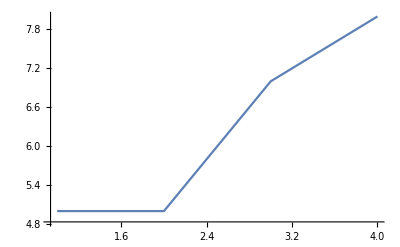

```mathematica
ListPlot[%,Joined->True]
```

```mathematica
FrontEndExecute[FrontEnd`AddMenuCommands["DuplicatePreviousOutput",{Delimiter,MenuItem["Make List",FrontEnd`KernelExecute[nb=SelectedNotebook[];
sel=NotebookRead[nb];
NotebookWrite[nb,Cell[BoxData[RowBox[{"{",sel,"}",","}]]]]],MenuKey["u",Modifiers->{"Control"}],System`MenuEvaluator->Automatic]}]]
```

```mathematica
List1=List[{1,802.13},

{2,305.78},

{3,414.53},

{4,373.82},

{5,487.19},

{6,304.56},

{7,774.57},

{8,634.8},

{9,759.33},

{10,678.97},

{11,277.88},

{12,705.75},

{13,548.93},

{14,111.91},

{15,546.1},

{16,485.38},

{17,686.18},

{18,341.19},

{19,723.17},

{20,572.1},

{21,395.53},

{22,755.82},

{23,630.76},

{24,652.08},

{25,475.11},

{26,684.99},

{27,840.07},

{28,894.33},

{29,762.01},

{30,450.56},

{31,810.12},

{32,833.88},

{33,741.06},

{34,197.03},

{35,794.48},

{36,629.79},

{37,407.31},

{38,540.07},

{39,723.43},

{40,618.44},

{41,310.7},

{42,633.66},

{43,507.74},

{44,686.27},

{45,671.95},

{46,890.12},

{47,511.44},

{48,696.75},

{49,519.82},

{50,776.61},

{51,934.89},

{52,357.46},

{53,549.9},

{54,402.25},

{55,748.98},

{56,780.17},

{57,663.58},

{58,276.26},

{59,180.97},

{60,757.28},

{61,443.95},

{62,893.44},

{63,469.93},

{64,623.55},

{65,452.37},

{66,439.56},

{67,705.07},

{68,596.85},

{69,817.68},

{70,432.16},

{71,744.23},

{72,682.85},

{73,885.16},

{74,875.23},

{75,689.88},

{76,600.03},

{77,731.46},

{78,846.79},

{79,770.04},

{80,499.11},

{81,558.48},

{82,680.91},

{83,663},

{84,846.99},

{85,614.58},

{86,341.58},

{87,528.24},

{88,599.1},

{89,434.35},

{90,678.38},

{91,743.15},

{92,458.45},

{93,601.52},

{94,299.84},

{95,722.22},

{96,610.53},

{97,590.23},

{98,436.06},

{99,445.4},

{100,306.13},

{101,282.12},

{102,307.64},

{103,928.98},

{104,846},

{105,812.06},

{106,551.77},

{107,591.55}]
```

(1 | 802.13
2 | 305.78
3 | 414.53
4 | 373.82
5 | 487.19
6 | 304.56
7 | 774.57
8 | 634.8
9 | 759.33
10 | 678.97
11 | 277.88
12 | 705.75
13 | 548.93
14 | 111.91
15 | 546.1
16 | 485.38
17 | 686.18
18 | 341.19
19 | 723.17
20 | 572.1
21 | 395.53
22 | 755.82
23 | 630.76
24 | 652.08
25 | 475.11
26 | 684.99
27 | 840.07
28 | 894.33
29 | 762.01
30 | 450.56
31 | 810.12
32 | 833.88
33 | 741.06
34 | 197.03
35 | 794.48
36 | 629.79
37 | 407.31
38 | 540.07
39 | 723.43
40 | 618.44
41 | 310.7
42 | 633.66
43 | 507.74
44 | 686.27
45 | 671.95
46 | 890.12
47 | 511.44
48 | 696.75
49 | 519.82
50 | 776.61
51 | 934.89
52 | 357.46
53 | 549.9
54 | 402.25
55 | 748.98
56 | 780.17
57 | 663.58
58 | 276.26
59 | 180.97
60 | 757.28
61 | 443.95
62 | 893.44
63 | 469.93
64 | 623.55
65 | 452.37
66 | 439.56
67 | 705.07
68 | 596.85
69 | 817.68
70 | 432.16
71 | 744.23
72 | 682.85
73 | 885.16
74 | 875.23
75 | 689.88
76 | 600.03
77 | 731.46
78 | 846.79
79 | 770.04
80 | 499.11
81 | 558.48
82 | 680.91
83 | 663
84 | 846.99
85 | 614.58
86 | 341.58
87 | 528.24
88 | 599.1
89 | 434.35
90 | 678.38
91 | 743.15
92 | 458.45
93 | 601.52
94 | 299.84
95 | 722.22
96 | 610.53
97 | 590.23
98 | 436.06
99 | 445.4
100 | 306.13
101 | 282.12
102 | 307.64
103 | 928.98
104 | 846
105 | 812.06
106 | 551.77
107 | 591.55)

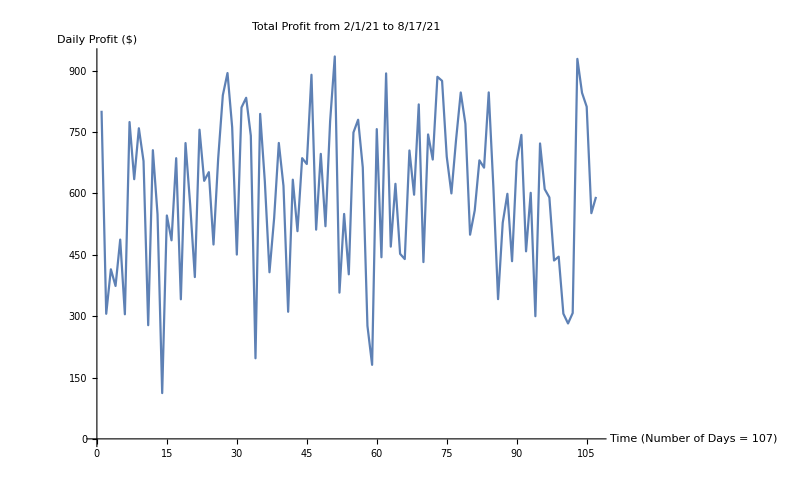

```mathematica
funct=ListPlot[List1,Joined-> True,AxesLabel-> {"Time (Number of Days = 107)","Daily Profit ($)"},PlotLabel->"Total Profit from 2/1/21 to 8/17/21",LabelStyle->{FontFamily->"Times",10,GrayLevel[0]}]
```

```mathematica
Max[List1]
```

934.89

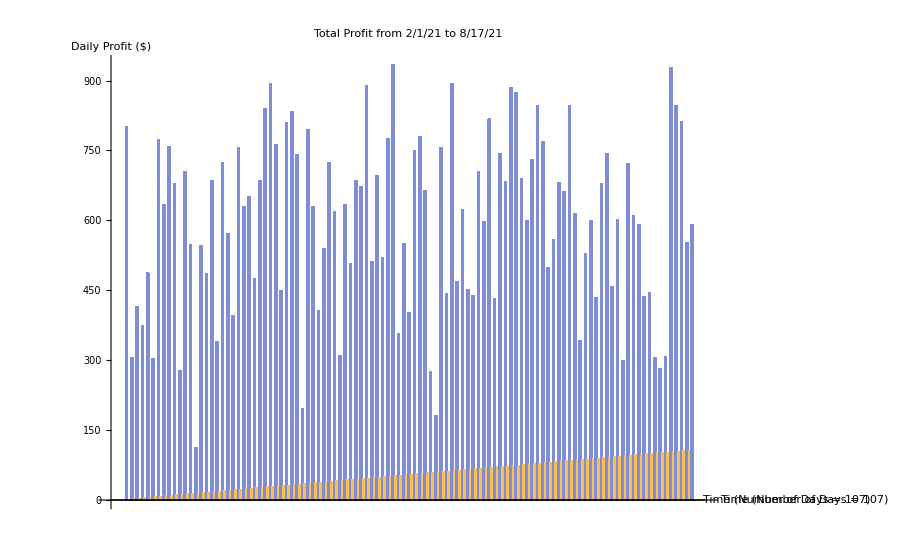

```mathematica
BarChart[List1,AxesLabel-> {"Time (Number of Days = 107)","Daily Profit ($)"},PlotLabel->"Total Profit from 2/1/21 to 8/17/21",LabelStyle->{FontFamily->"Times",10,GrayLevel[0]}]
```

```mathematica
points={{1,802.13},

{2,305.78},

{3,414.53},

{4,373.82},

{5,487.19},

{6,304.56},

{7,774.57},

{8,634.8},

{9,759.33},

{10,678.97},

{11,277.88},

{12,705.75},

{13,548.93},

{14,111.91},

{15,546.1},

{16,485.38},

{17,686.18},

{18,341.19},

{19,723.17},

{20,572.1},

{21,395.53},

{22,755.82},

{23,630.76},

{24,652.08},

{25,475.11},

{26,684.99},

{27,840.07},

{28,894.33},

{29,762.01},

{30,450.56},

{31,810.12},

{32,833.88},

{33,741.06},

{34,197.03},

{35,794.48},

{36,629.79},

{37,407.31},

{38,540.07},

{39,723.43},

{40,618.44},

{41,310.7},

{42,633.66},

{43,507.74},

{44,686.27},

{45,671.95},

{46,890.12},

{47,511.44},

{48,696.75},

{49,519.82},

{50,776.61},

{51,934.89},

{52,357.46},

{53,549.9},

{54,402.25},

{55,748.98},

{56,780.17},

{57,663.58},

{58,276.26},

{59,180.97},

{60,757.28},

{61,443.95},

{62,893.44},

{63,469.93},

{64,623.55},

{65,452.37},

{66,439.56},

{67,705.07},

{68,596.85},

{69,817.68},

{70,432.16},

{71,744.23},

{72,682.85},

{73,885.16},

{74,875.23},

{75,689.88},

{76,600.03},

{77,731.46},

{78,846.79},

{79,770.04},

{80,499.11},

{81,558.48},

{82,680.91},

{83,663},

{84,846.99},

{85,614.58},

{86,341.58},

{87,528.24},

{88,599.1},

{89,434.35},

{90,678.38},

{91,743.15},

{92,458.45},

{93,601.52},

{94,299.84},

{95,722.22},

{96,610.53},

{97,590.23},

{98,436.06},

{99,445.4},

{100,306.13},

{101,282.12},

{102,307.64},

{103,928.98},

{104,846},

{105,812.06},

{106,551.77},

{107,591.55}}
```

(1 | 802.13
2 | 305.78
3 | 414.53
4 | 373.82
5 | 487.19
6 | 304.56
7 | 774.57
8 | 634.8
9 | 759.33
10 | 678.97
11 | 277.88
12 | 705.75
13 | 548.93
14 | 111.91
15 | 546.1
16 | 485.38
17 | 686.18
18 | 341.19
19 | 723.17
20 | 572.1
21 | 395.53
22 | 755.82
23 | 630.76
24 | 652.08
25 | 475.11
26 | 684.99
27 | 840.07
28 | 894.33
29 | 762.01
30 | 450.56
31 | 810.12
32 | 833.88
33 | 741.06
34 | 197.03
35 | 794.48
36 | 629.79
37 | 407.31
38 | 540.07
39 | 723.43
40 | 618.44
41 | 310.7
42 | 633.66
43 | 507.74
44 | 686.27
45 | 671.95
46 | 890.12
47 | 511.44
48 | 696.75
49 | 519.82
50 | 776.61
51 | 934.89
52 | 357.46
53 | 549.9
54 | 402.25
55 | 748.98
56 | 780.17
57 | 663.58
58 | 276.26
59 | 180.97
60 | 757.28
61 | 443.95
62 | 893.44
63 | 469.93
64 | 623.55
65 | 452.37
66 | 439.56
67 | 705.07
68 | 596.85
69 | 817.68
70 | 432.16
71 | 744.23
72 | 682.85
73 | 885.16
74 | 875.23
75 | 689.88
76 | 600.03
77 | 731.46
78 | 846.79
79 | 770.04
80 | 499.11
81 | 558.48
82 | 680.91
83 | 663
84 | 846.99
85 | 614.58
86 | 341.58
87 | 528.24
88 | 599.1
89 | 434.35
90 | 678.38
91 | 743.15
92 | 458.45
93 | 601.52
94 | 299.84
95 | 722.22
96 | 610.53
97 | 590.23
98 | 436.06
99 | 445.4
100 | 306.13
101 | 282.12
102 | 307.64
103 | 928.98
104 | 846
105 | 812.06
106 | 551.77
107 | 591.55)

```mathematica
ifun=Interpolation[points]
```

InterpolatingFunction[…]

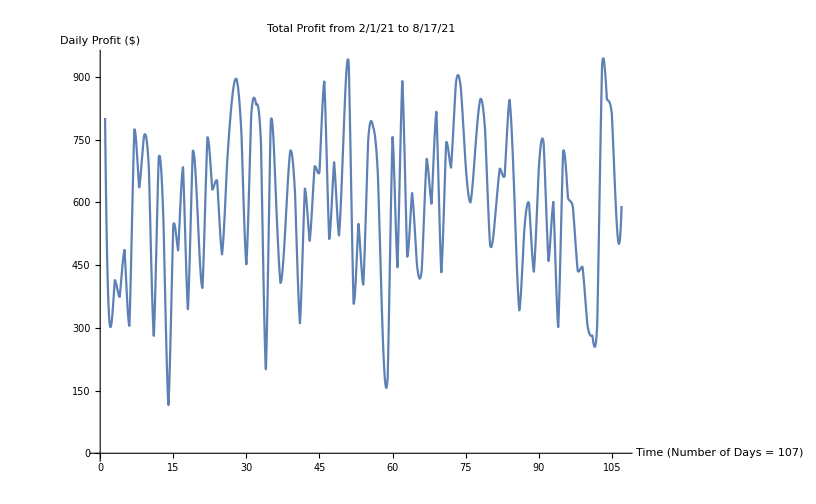

```mathematica
Plot[ifun[x],{x,1.,107.},AxesLabel-> {"Time (Number of Days = 107)","Daily Profit ($)"},PlotLabel->"Total Profit from 2/1/21 to 8/17/21",LabelStyle->{FontFamily->"Times",10,GrayLevel[0]},AxesOrigin->{0,0}]
```

```mathematica
Integrate[ifun[x], {x,40,60}]
```

11759.2

## Scratch

```mathematica
Plus[934.89,928.98,894.33,893.44,890.12,887.30,885.16,875.23,846.99,846.79,846.00,840.07,833.88,817.68,812.06,810.12,802.13,794.48,790.25,781.58,780.17,776.61,774.57,770.04,762.01,759.33,757.28,755.82,748.98,744.23,743.15,741.06,731.46,723.43,723.17,722.22,705.75,705.07,696.75,689.88,686.27,686.18,684.99,682.85,680.91,678.38,671.95,663.58,663.00,652.08,634.80,633.66,630.76,629.79,623.55,618.44,614.58,610.53,601.52,600.03,599.10,596.85,591.55,590.23,572.10,558.48,551.77,549.90,548.93,546.10,540.07,528.24,519.82,511.44,507.74,499.11,487.19,485.38,475.11,469.93,458.45,452.37,450.56,445.40,443.95,439.56,436.06,434.35,432.16,430.21,414.53,407.31,402.25,395.53,373.82,357.46,341.58,341.19,310.70,307.64,306.13,305.78,304.56,299.84,282.12,277.88,276.26,243.20,197.03,180.97,111.91]
```

66360.1

```mathematica
(934.89+928.98)/TotalDaysLen
(894.33+893.44+890.12+887.30+885.16+875.23+846.99+846.79+846.00+840.07+833.88+817.68+812.06+810.12+802.13)/TotalDaysLen
(794.48+790.25+781.58+780.17+776.61+774.57+770.04+762.01+759.33+757.28+755.82+748.98+744.23+743.15+741.06+731.46+723.43+723.17+722.22+705.75+705.07)/TotalDaysLen
(696.75+689.88+686.27+686.18+684.99+682.85+680.91+678.38+671.95+663.58+663.00+652.08+634.80+633.66+630.76+629.79+623.55+618.44+614.58+610.53+601.52+600.03)/TotalDaysLen
(599.10+596.85+591.55+590.23+572.10+558.48+551.77+549.90+548.93+546.10+540.07+528.24+519.82+511.44+507.74)/TotalDaysLen
(499.11+487.19+485.38+475.11+469.93+458.45+452.37+450.56+445.40+443.95+439.56+436.06+434.35+432.16+430.21+414.53+407.31+402.25)/TotalDaysLen
(395.53+373.82+357.46+341.58+341.19+310.70+307.64+306.13+305.78+304.56)/TotalDaysLen
(299.84+282.12+277.88+276.26+243.20 )/ TotalDaysLen
(197.03+180.97+111.91 )/ TotalDaysLen
```

16.7916

115.147

142.258

129.139

74.8858

72.6476

30.1296

12.4261

4.4136

```mathematica
1/25/21 100

1/26/21 430.21

1/26/21 0.01

1/27/21 243.2

1/28/21 781.58

1/29/21 790.25

2/1/21 802.13

2/1/21 305.78

2/4/21 414.53

2/5/21 373.82

2/8/21 487.19

2/8/21 304.56

2/12/21 774.57

2/16/21 634.8

2/16/21 759.33

2/18/21 678.97

2/19/21 277.88

2/22/21 705.75

2/22/21 196

2/22/21 100

2/22/21 548.93

2/23/21 111.91

2/25/21 546.1

2/26/21 485.38

3/1/21 686.18

3/1/21 341.19

3/4/21 723.17

3/8/21 572.1

3/10/21 395.53

3/11/21 755.82

3/12/21 630.76

3/15/21 652.08

3/16/21 475.11

3/18/21 684.99

3/19/21 840.07

3/22/21 894.33

3/22/21 762.01

3/24/21 16451

3/25/21 450.56

3/26/21 810.12

3/29/21 833.88

3/29/21 741.06

4/1/21 197.03

4/2/21 794.48

4/5/21 629.79

4/5/21 407.31

4/8/21 540.07

4/9/21 723.43

4/12/21 618.44

4/12/21 310.7

4/15/21 633.66

4/16/21 507.74

4/19/21 686.27

4/19/21 671.95

4/22/21 890.12

4/23/21 511.44

4/26/21 696.75

4/26/21 519.82

4/28/21 776.61

4/29/21 934.89

4/30/21-24.98

4/30/21 357.46

5/3/21 549.9

5/3/21 402.25

5/6/21 748.98

5/7/21 780.17

5/10/21 663.58

5/10/21 276.26

5/14/21 180.97

5/17/21 757.28

5/19/21 443.95

5/20/21 893.44

5/21/21 469.93

5/24/21 623.55

5/24/21 452.37

5/26/21 439.56

5/27/21 705.07

5/28/21 596.85

6/3/21 817.68

6/4/21 432.16

6/4/21 418.47

6/7/21 744.23

6/7/21 682.85

6/7/21 418.47

6/9/21 885.16

6/10/21 875.23

6/11/21 689.88

6/17/21 600.03

6/18/21 731.46

6/21/21 846.79

6/21/21 770.04

6/21/21 16.34

6/24/21 499.11

6/25/21 558.48

6/28/21 680.91

7/2/21 663

7/6/21 846.99

7/6/21 614.58

7/7/21 6991.4

7/7/21 1450

7/8/21 341.58

7/9/21 528.24

7/12/21 599.1

7/12/21 434.35

7/14/21 678.38

7/15/21 743.15

7/16/21 458.45

7/19/21 601.52

7/22/21 299.84

7/23/21 722.22

7/26/21 610.53

7/26/21 590.23

7/29/21 436.06

7/29/21 134.75

7/30/21 445.4

8/2/21 306.13

8/2/21 282.12

8/10/21 307.64

8/12/21 928.98

8/13/21 68.3

8/13/21 846

8/16/21 812.06

8/16/21 551.77

8/17/21 591.55
```

```mathematica
FrontEndExecute[FrontEnd`AddMenuCommands["DuplicatePreviousOutput",{Delimiter,MenuItem["Make List",FrontEnd`KernelExecute[nb=SelectedNotebook[];
sel=NotebookRead[nb];
NotebookWrite[nb,Cell[BoxData[RowBox[{"{",sel,"}",","}]]]]],MenuKey["u",Modifiers->{"Control"}],System`MenuEvaluator->Automatic]}]]
```